```mathematica
ClearAll["Global`*"]
Needs["ComputerArithmetic`"]
mypath = "/home/leon/Dropbox/Mathematica/Space/Exp/Global";
CreateDirectory[mypath] ;

linearmesh[a_, b_, n_Integer /; n > 1] := Range[a, b, (b - a)/(n - 1)] ;
(* Parameters *)
PARAM := ( 
  	Jee = 1.1 ; Jei = 1.5 ; Jie = 1.8 ; Jii = 1.8 ;
  	Ie0 = .85 ; Ii0 = .85 ;
  	Γe0 = 0 ; Γi0 = .1 ;
  	σ0 = .1 ;
  	λe = .125 ; λi = .075 ; 
  	L = 3 ;
) ;

J = { {Jee,-Jei}, {Jie,-Jii}} ;
I0 = {Ie0, Ii0} ;

G[x_,σ_] := Exp[-x^2/2/σ^2]/Sqrt[2 π] / σ ;
W[x_,λ_] := Exp[-Abs[x]/λ]/λ ;

Jx[x_] := { { Jee W[x,λe] ,-Jei W[x,λi]}, {Jie W[x,λe],-Jii W[x,λi]}} ;
Iprtr[x_] := {0, Γi0 G[x,σ0]} ;￼

JFT[k_] := FourierTransform[Jx[x],x,k] ;

r0 = Simplify[LinearSolve[JFT[0],-I0], λe>0 && λi>0 && σ0>0]/Sqrt[2 Pi] ;
IextFT[k_] = FourierTransform[Iprtr[x],x,k] ;
mFT[k_] = Simplify[LinearSolve[JFT[k],-IextFT[k]], λe>0 && λi>0 && σ0>0] ;
r[x_] = r0 + InverseFourierTransform[mFT[k],k,x] /Sqrt[2 Pi]
Γmax = First[Γi0 /. Solve[r[0][[1]]/r0[[1]]==0, Γi0] ]
ΓmaxI = First[Γi0 /. Solve[r[0][[2]]/r0[[2]]==0, Γi0] ]
```

CreateDirectory::filex: /home/leon/Dropbox/Mathematica/Space/Exp/Global already exists.

￼

{(-Ii0 Jei+Ie0 Jii)/(2 Jei Jie-2 Jee Jii)-(ⅇ^(-x^2/(2 σ0^2)) Jei Γi0 (-x^2 λe^2+λe^2 σ0^2+σ0^4))/(2 (Jei Jie-Jee Jii) √(2 π) σ0^4 √(σ0^2)),(-Ii0 Jee+Ie0 Jie)/(2 Jei Jie-2 Jee Jii)+(ⅇ^(-x^2/(2 σ0^2)) Jee Γi0 (-x^2 λi^2+λi^2 σ0^2+σ0^4))/(2 (-Jei Jie+Jee Jii) √(2 π) σ0^4 √(σ0^2))}

-((Ii0 Jei-Ie0 Jii) √(2 π) (σ0^2)^(3/2))/(Jei (λe^2+σ0^2))

-((Ii0 Jee-Ie0 Jie) √(2 π) (σ0^2)^(3/2))/(Jee (λi^2+σ0^2))

```mathematica
NormR[x_,Γi0_]:={(-Ii0 Jei+Ie0 Jii)/(2 Jei Jie-2 Jee Jii)-(ⅇ^(-x^2/(2 σ0^2)) Jei Γi0 (-x^2 λe^2+λe^2 σ0^2+σ0^4))/(2 (Jei Jie-Jee Jii) √(2 π) σ0^4 √(σ0^2)),(-Ii0 Jee+Ie0 Jie)/(2 Jei Jie-2 Jee Jii)+(ⅇ^(-x^2/(2 σ0^2)) Jee Γi0 (-x^2 λi^2+λi^2 σ0^2+σ0^4))/(2 (-Jei Jie+Jee Jii) √(2 π) σ0^4 √(σ0^2))}
```

```mathematica
D[NormR[x,Γi0],Γi0]
```

{-(ⅇ^(-x^2/(2 σ0^2)) Jei (-x^2 λe^2+λe^2 σ0^2+σ0^4))/(2 (Jei Jie-Jee Jii) √(2 π) σ0^4 √(σ0^2)),(ⅇ^(-x^2/(2 σ0^2)) Jee (-x^2 λi^2+λi^2 σ0^2+σ0^4))/(2 (-Jei Jie+Jee Jii) √(2 π) σ0^4 √(σ0^2))}

```mathematica
xM = x/. Last[Solve[r'[x][[1]]==0,x]]
Simplify[r[xM]/r0][[1]]
```

(σ0 √(3 λe^2+σ0^2))/λe

(Ii0 Jei σ0^4-Ie0 Jii σ0^4-ⅇ^(-3/2-σ0^2/(2 λe^2)) Jei √(2/π) Γi0 λe^2 √(σ0^2))/((Ii0 Jei-Ie0 Jii) σ0^4)

```mathematica
xM = x/. Last[Solve[r'[x][[2]]==0,x]]
Simplify[r[xM]/r0][[2]]
```

(σ0 √(3 λi^2+σ0^2))/λi

(Ii0 Jee σ0^4-Ie0 Jie σ0^4-ⅇ^(-3/2-σ0^2/(2 λi^2)) Jee √(2/π) Γi0 λi^2 √(σ0^2))/((Ii0 Jee-Ie0 Jie) σ0^4)

```mathematica
solve[-(ⅇ^(-x^2/(2 σ0^2)) Jee x Γi0 λi^2)/((-Jei Jie+Jee Jii) σ0^4 √(σ0^2))-(ⅇ^(-x^2/(2 σ0^2)) Jee x Γi0 (-x^2 λi^2+λi^2 σ0^2+σ0^4))/(2 (-Jei Jie+Jee Jii) σ0^6 √(σ0^2))==0,x]
```

solve[-(ⅇ^(-x^2/(2 σ0^2)) Jee x Γi0 λi^2)/((-Jei Jie+Jee Jii) σ0^4 √(σ0^2))-(ⅇ^(-x^2/(2 σ0^2)) Jee x Γi0 (-x^2 λi^2+λi^2 σ0^2+σ0^4))/(2 (-Jei Jie+Jee Jii) σ0^6 √(σ0^2))==0,x]

```mathematica
0
r'[x]
```

0

{(ⅇ^(-x^2/(2 σ0^2)) Jei x Γi0 λe^2)/((Jei Jie-Jee Jii) σ0^4 √(σ0^2))+(ⅇ^(-x^2/(2 σ0^2)) Jei x Γi0 (-x^2 λe^2+λe^2 σ0^2+σ0^4))/(2 (Jei Jie-Jee Jii) σ0^6 √(σ0^2)),-(ⅇ^(-x^2/(2 σ0^2)) Jee x Γi0 λi^2)/((-Jei Jie+Jee Jii) σ0^4 √(σ0^2))-(ⅇ^(-x^2/(2 σ0^2)) Jee x Γi0 (-x^2 λi^2+λi^2 σ0^2+σ0^4))/(2 (-Jei Jie+Jee Jii) σ0^6 √(σ0^2))}

```mathematica
PARAM
Γmax
```

0.00663415

```mathematica
normR[x_,σ0_,Γi0_]:={((2 Jei Jie-2 Jee Jii) ((-Ii0 Jei+Ie0 Jii)/(2 Jei Jie-2 Jee Jii)-(ⅇ^(-x^2/(2 σ0^2)) Jei Γi0 (-x^2 λe^2+λe^2 σ0^2+σ0^4))/(2 (Jei Jie-Jee Jii) σ0^4 √(σ0^2))))/(-Ii0 Jei+Ie0 Jii),((2 Jei Jie-2 Jee Jii) ((-Ii0 Jee+Ie0 Jie)/(2 Jei Jie-2 Jee Jii)+(ⅇ^(-x^2/(2 σ0^2)) Jee Γi0 (-x^2 λi^2+λi^2 σ0^2+σ0^4))/(2 (-Jei Jie+Jee Jii) σ0^4 √(σ0^2))))/(-Ii0 Jee+Ie0 Jie)}
```

```mathematica
ΓmaxVsλe := (
	ΓmaxVsλeList = {} ;
	For[l=1,l<=Length[λeList],l++,
		λe = λeList[[l]] ; 
		max = Γmax ;
		AppendTo[ΓmaxVsλeList,max] ;
	] ;
)

ΓmaxVsσ0 := (
	ΓmaxVsσ0List = {} ;
	For[l=1,l<=Length[σ0List],l++,
		σ0 = σ0List[[l]] ; 
		max = Γmax ;
		AppendTo[ΓmaxVsσ0List,max] ;
	] ;
)
```

```mathematica
PARAM
σ0 = .15 ;
λeList = linearmesh[.01,.375,20] // N 
λi = .075 ;
ΓmaxVsλe
ΓmaxVsλeList
```

{0.01,0.0292105,0.0484211,0.0676316,0.0868421,0.106053,0.125263,0.144474,0.163684,0.182895,0.202105,0.221316,0.240526,0.259737,0.278947,0.298158,0.317368,0.336579,0.355789,0.375}

{0.0253872,0.0245683,0.0230936,0.0211919,0.0190985,0.0170014,0.0150232,0.0132284,0.0116397,0.0102546,0.00905732,0.00802664,0.00714038,0.00637761,0.00571968,0.00515045,0.0046562,0.00422542,0.00384845,0.00351724}

```mathematica
dataΓvsλe = Transpose@{4 λeList,ΓmaxVsλeList} ;
pltΓvsλe = ListLinePlot[dataΓvsλe,FrameLabel->{"4 λe","Γmax"},
					Frame->{{True,False},{True,False}},
					PlotRange->{{0,L/2},Automatic},PlotMarkers->{●,12},PlotStyle->Black]
```

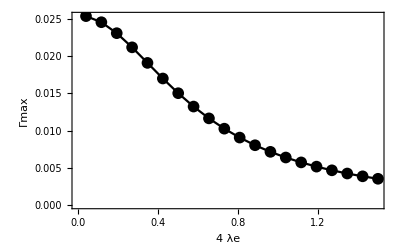

```mathematica
σ0=0.15
```

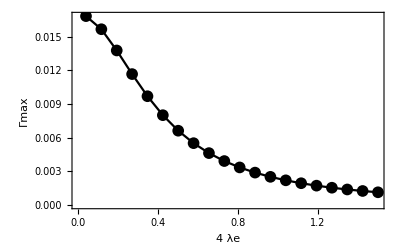

```mathematica
σ0=0.1
```

```mathematica
fileName = StringJoin[{mypath,"/G0maxVsCie_Cff_",ToString[NumberForm[σ0,{1,4}]],".dat"}] 
Export[fileName,data,"Table"] ;
```

/home/leon/Dropbox/Mathematica/Space/Exp/Global/G0maxVsCie_Cff_0.2000.dat

```mathematica
PARAM
σ0List = linearmesh[.01,.375,20] // N 
λe = .125 ; λi = .075 ;
ΓmaxVsσ0
ΓmaxVsσ0List
```

{0.01,0.0292105,0.0484211,0.0676316,0.0868421,0.106053,0.125263,0.144474,0.163684,0.182895,0.202105,0.221316,0.240526,0.259737,0.278947,0.298158,0.317368,0.336579,0.355789,0.375}

{0.0000108108,0.000257132,0.00107402,0.00260356,0.00480594,0.00754589,0.0106698,0.0140459,0.0175762,0.0211928,0.0248515,0.0285243,0.0321944,0.0358517,0.039491,0.0431097,0.046707,0.0502831,0.0538387,0.057375}

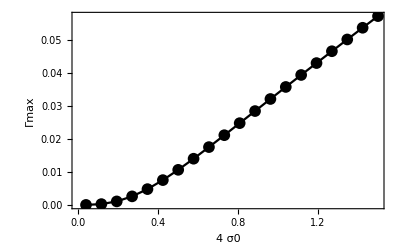

```mathematica
dataΓmaxVsσ0 = Transpose@{4 σ0List,ΓmaxVsσ0List} ;
PltΓmaxVsσ0 = ListLinePlot[dataΓmaxVsσ0,FrameLabel->{"4 σ0","Γmax"},
					Frame->{{True,False},{True,False}},
					PlotRange->{{0,L/2},Automatic},PlotMarkers->{●,12},PlotStyle->Black]
```

```mathematica
fileName = StringJoin[{mypath,"/G0maxVsCff",".dat"}] 
Export[fileName,data,"Table"] ;
```

/home/leon/Dropbox/Mathematica/Space/Exp/Global/G0maxVsCff.dat

0.0166293

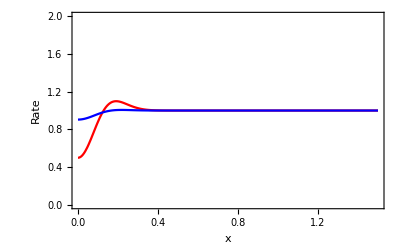

/home/leon/Dropbox/Mathematica/Space/Exp/Global/Profile_Cff_0.1000_G0_0.0083.dat

```mathematica
PARAM
σ0=0.1 ; Γi0=Γmax/2 ;
Γmax
Plot[{Part[r[x],1]/r0[[1]],Part[r[x],2]/r0[[2]]}, {x, 0, L/2}, AxesOrigin -> {0, -0.1},
   	Frame -> {{True, False}, {True, False}}, FrameLabel -> {"x", "Rate"}, PlotStyle -> {Red,Blue},PlotRange->{0,2}] 
data = Table[{x,Part[r[x],1]/r0[[1]],Part[r[x],2]/r0[[2]]},{x,0,L/2,.01}] ;
fileName = StringJoin[{mypath,"/Profile_Cff_",ToString[NumberForm[σ0,{4,4}]],"_G0_",ToString[NumberForm[Γi0,{4,4}]],".dat"}] 
Export[fileName,data,"Table"] ;
```

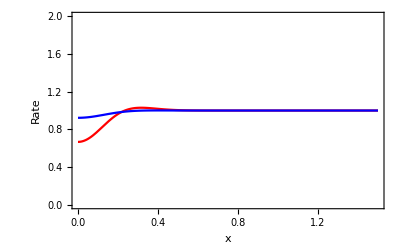

```mathematica
σ0=0.15 ;Γi0=0.005 ;
```

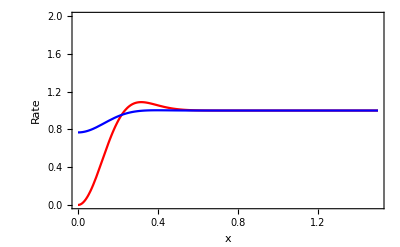

```mathematica
σ0=0.15 ; Γi0=Γmax ;
```

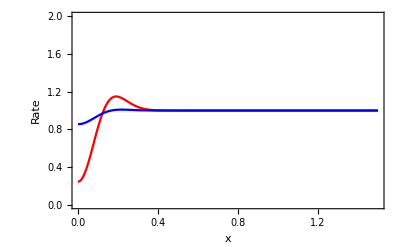

```mathematica
σ0=0.1 ; Γi0=0.005 ;
```

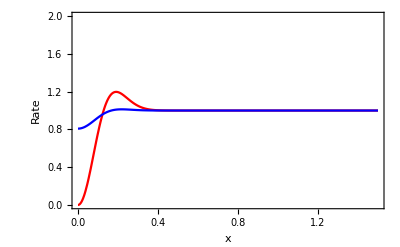

```mathematica
σ0=0.1 ; Γi0=Γmax;
```

```mathematica
PARAM
σ0 Sqrt[1+σ0^2/λe^2]
σ0 Sqrt[1+σ0^2/λi^2]
```

0.128062

0.166667

```mathematica
data = Table[{x,Part[r[x],1]/r0[[1]],Part[r[x],2]/r0[[2]]},{x,0,L/2,.01}] ;
fileName = StringJoin[{mypath,"/Profile_Cff_",ToString[NumberForm[σ0,{1,4}]],"_G0_",ToString[NumberForm[Γi0,{1,4}]],".dat"}] 
Export[fileName,data,"Table"] ;
```

/home/leon/Dropbox/Mathematica/Space/Exp/Global/Profile_Cff_0.2000_G0_0.0200.dat

```mathematica
r[0][[1]]/r0[[1]]
```

1.56737×10^-16

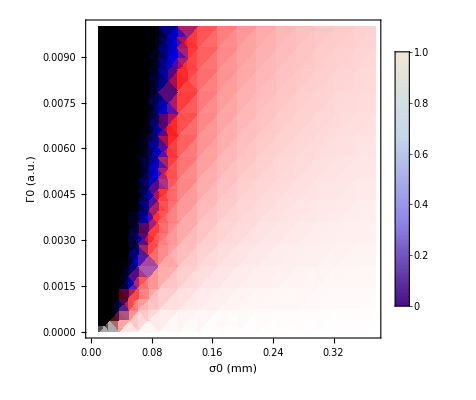

```mathematica
rCenter[σ0_,Γi0_] := normR[0,σ0,Γi0]
PARAM
DensityPlot[rCenter[σ0,Γi0][[1]],{σ0,.01,.375},{Γi0,0,.01}, ColorFunction -> (If[# < 0, Darker[Blue, Abs[#]],
Lighter[Red, #]] &), ColorFunctionScaling -> False, FrameLabel -> {"σ0 (mm)", "Γ0 (a.u.)"},
PlotLegends->BarLegend[LegendLabel->"Norm. r_E(0)"],PlotRange->{-1000,1}]
```

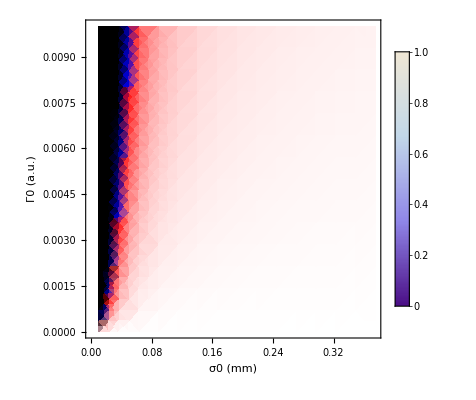

```mathematica
DensityPlot[rCenter[σ0,Γi0][[2]],{σ0,.01,.375},{Γi0,0,.01}, FrameLabel -> {"σ0 (mm)", "Γ0 (a.u.)"},
PlotLegends->BarLegend[LegendLabel->"Norm. r_I(0)"], ColorFunction -> (If[# < 0, Darker[Blue, Abs[#]],
Lighter[Red, #]] &), ColorFunctionScaling -> False ,PlotRange->{-1000,1}]
```

```mathematica
normR[x_,σ0_,Γi0_]:={((2 Jei Jie-2 Jee Jii) ((-Ii0 Jei+Ie0 Jii)/(2 Jei Jie-2 Jee Jii)-(ⅇ^(-x^2/(2 σ0^2)) Jei Γi0 (-x^2 λe^2+λe^2 σ0^2+σ0^4))/(2 (Jei Jie-Jee Jii) σ0^4 √(σ0^2))))/(-Ii0 Jei+Ie0 Jii),
((2 Jei Jie-2 Jee Jii) ((-Ii0 Jee+Ie0 Jie)/(2 Jei Jie-2 Jee Jii)+(ⅇ^(-x^2/(2 σ0^2)) Jee Γi0 (-x^2 λi^2+λi^2 σ0^2+σ0^4))/(2 (-Jei Jie+Jee Jii) σ0^4 √(σ0^2))))/(-Ii0 Jee+Ie0 Jie)}
```

```mathematica
r0VsΓ0 := (
	rE0VsΓ0List = {} ;
	rI0VsΓ0List = {} ;
	For[l=1,l<=Length[Γ0List],l++,
		Γi0 = Γ0List[[l]] ; 
		rE0 = normR[0,σ0,Γi0][[1]] ;
		rI0 = normR[0,σ0,Γi0][[2]] ;
		AppendTo[rE0VsΓ0List,rE0] ;
		AppendTo[rI0VsΓ0List,rI0] ;
	] ;
)
```

```mathematica
PARAM
σ0 = .05 ;
Γ0List = linearmesh[0,Γmax,20] // N 
r0VsΓ0
rE0VsΓ0List
rI0VsΓ0List
```

{0.,0.000061706,0.000123412,0.000185118,0.000246824,0.00030853,0.000370236,0.000431942,0.000493648,0.000555354,0.00061706,0.000678766,0.000740472,0.000802178,0.000863884,0.00092559,0.000987296,0.001049,0.00111071,0.00117241}

{1.,0.947368,0.894737,0.842105,0.789474,0.736842,0.684211,0.631579,0.578947,0.526316,0.473684,0.421053,0.368421,0.315789,0.263158,0.210526,0.157895,0.105263,0.0526316,0.}

{1.,0.992585,0.98517,0.977755,0.97034,0.962925,0.955509,0.948094,0.940679,0.933264,0.925849,0.918434,0.911019,0.903604,0.896189,0.888774,0.881359,0.873943,0.866528,0.859113}

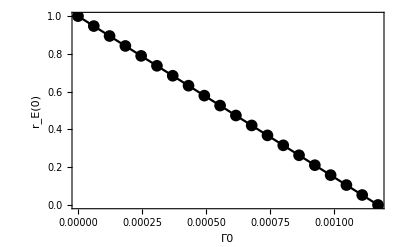

```mathematica
datarE0VsΓ0 = Transpose@{Γ0List,rE0VsΓ0List} ;
PltrE0VsΓ0 = ListLinePlot[datarE0VsΓ0,FrameLabel->{"Γ0","r_E(0)"},
					Frame->{{True,False},{True,False}},
					PlotRange->{{0,Γmax},Automatic},PlotMarkers->{●,12},PlotStyle->Black]
```

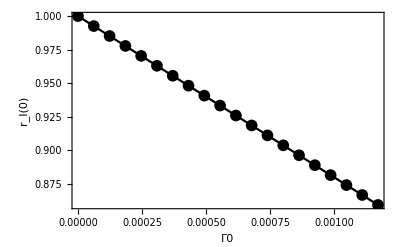

```mathematica
datarI0VsΓ0 = Transpose@{Γ0List,rI0VsΓ0List} ;
PltrI0VsΓ0 = ListLinePlot[datarI0VsΓ0,FrameLabel->{"Γ0","r_I(0)"},
					Frame->{{True,False},{True,False}},
					PlotRange->{{0,Γmax},Automatic},PlotMarkers->{●,12},PlotStyle->Black]
```

```mathematica
r0Vsσ0 := (
	rE0Vsσ0List = {} ;
	rI0Vsσ0List = {} ;
	For[l=1,l<=Length[σ0List],l++,
		σ0 = σ0List[[l]] ; 
		rE0 = normR[0,σ0,Γi0][[1]] ;
		rI0 = normR[0,σ0,Γi0][[2]] ;
		AppendTo[rE0Vsσ0List,rE0] ;
		AppendTo[rI0Vsσ0List,rI0] ;
	] ;
)
```

```mathematica
PARAM
Γi0 = .001 ;
σ0List = linearmesh[.05,.375,20] // N 
r0Vsσ0
rE0Vsσ0List
rI0Vsσ0List
```

{0.05,0.0671053,0.0842105,0.101316,0.118421,0.135526,0.152632,0.169737,0.186842,0.203947,0.221053,0.238158,0.255263,0.272368,0.289474,0.306579,0.323684,0.340789,0.357895,0.375}

{0.147059,0.608182,0.776235,0.853563,0.894981,0.919673,0.935612,0.946549,0.954426,0.960323,0.96488,0.968496,0.97143,0.973854,0.97589,0.977623,0.979117,0.980417,0.981559,0.982571}

{0.879832,0.938037,0.960632,0.971753,0.978126,0.982181,0.984963,0.986982,0.988511,0.989709,0.990674,0.991467,0.992132,0.992698,0.993185,0.993609,0.993982,0.994312,0.994608,0.994873}

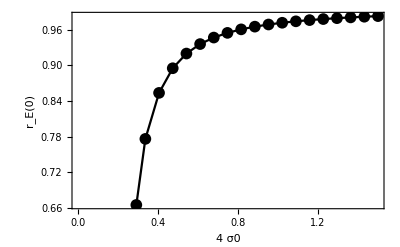

```mathematica
datarE0Vsσ0 = Transpose@{4 σ0List,rE0Vsσ0List} ;
PltrE0Vsσ0 = ListLinePlot[datarE0Vsσ0,FrameLabel->{"4 σ0","r_E(0)"},
					Frame->{{True,False},{True,False}},
					PlotRange->{{0,L/2},Automatic},PlotMarkers->{●,12},PlotStyle->Black]
```

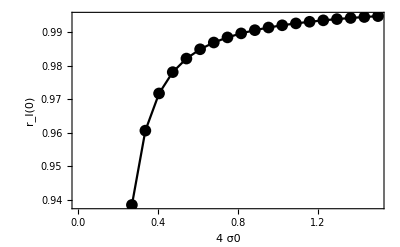

```mathematica
datarI0Vsσ0 = Transpose@{4 σ0List,rI0Vsσ0List} ;
PltrI0Vsσ0 = ListLinePlot[datarI0Vsσ0,FrameLabel->{"4 σ0","r_I(0)"},
					Frame->{{True,False},{True,False}},
					PlotRange->{{0,L/2},Automatic},PlotMarkers->{●,12},PlotStyle->Black]
```